```mathematica
Needs["HierarchicalClustering`"]
SetOptions[{Plot,MatrixPlot},ImageSize->200{1,1}];
```

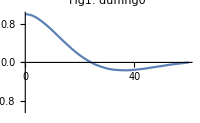

```mathematica
Module[{tmax=60,ϵ=0,δ=10,γ=1/10},
duffing0=NDSolveValue[{100y''[t]+δ y'[t]+y[t]+ϵ (y[t])^3==γ Cos[t],y[0]==1,y'[0]==0},y,{t,0,tmax}];
Plot[duffing0[t],{t,0.,tmax},PlotLabel->"Fig1. duffing0",PlotRange->{{0,tmax},{-1,1}}]]
```

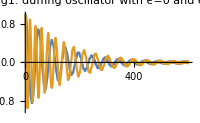

```mathematica
Module[{tmax=600,ϵ,δ=1,γ=1,μ=60},
ϵ=0;
duffing0=NDSolveValue[{μ y''[t]+δ y'[t]+y[t]+ϵ (y[t])^3==γ Cos[t],y[0]==1,y'[0]==0},y,{t,0,tmax}];
ϵ=10;
duffing5=NDSolveValue[{μ y''[t]+δ y'[t]+y[t]+ϵ (y[t])^3==γ Cos[t],y[0]==1,y'[0]==0},y,{t,0,tmax}];
Plot[{duffing0[t],duffing5[t]},{t,0.,tmax},PlotLabel->"Fig1. duffing oscillator with ϵ=0 and ϵ=5",PlotRange->{{0,tmax},{-1,1}},PlotLegends->{"ϵ=0","ϵ=5"}]]
```

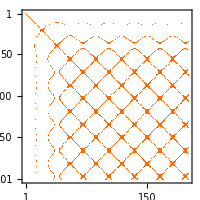
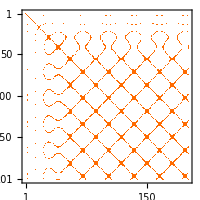
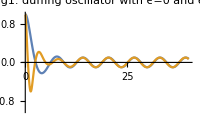

```mathematica
Module[{tmax=40,ϵ,δ=1,γ=1/10,μ=1,sz=0.2,nn,startStep,endStep},
ϵ=0;
duffing0=NDSolveValue[{μ y''[t]+δ y'[t]+y[t]+ϵ(y[t])^3==γ Cos[t],y[0]==1,y'[0]==0},y,{t,0,tmax}];
ϵ=10;
duffing5=NDSolveValue[{μ y''[t]+δ y'[t]+y[t]+ϵ (y[t])^3==γ Cos[t],y[0]==1,y'[0]==0},y,{t,0,tmax}];
Plot[{duffing0[t],duffing5[t]},{t,0.,tmax},PlotLabel->"Fig1. duffing oscillator with ϵ=0 and ϵ=5",PlotRange->{{0,tmax},{-1,1}},PlotLegends->{"ϵ=0","ϵ=5"}]

With[{stepSize=sz,end=tmax},MatrixPlot[UnitStep[0.0001-DistanceMatrix[duffing0[Range[0,end,stepSize]]]]]
MatrixPlot[UnitStep[0.0001-DistanceMatrix[duffing5[Range[0,end,stepSize]]]]]
]
]
```

```mathematica
sz=40;
nn=0.00001;
startStep=0;
endStep=40;
With[{stepSize=sz,end=tmax},MatrixPlot[UnitStep[nn-DistanceMatrix[duffing0[Range[startStep,endStep,stepSize]]]]]]

With[{stepSize=0.4,end=tmax},MatrixPlot[UnitStep[nn-DistanceMatrix[duffing5[Range[startStep,endStep,stepSize]]]]]]
```